```mathematica
(19000 0.907)
```

17233.

```mathematica
<<Units`
```

```mathematica
Convert[1 Feet,1 Inch]
```

12 Inch

```mathematica
Convert[]
```

```mathematica
Solve[2000==9150(gm-8.9) 0.052,gm]
```

{{gm→13.1034}}

```mathematica
13.1 0.052
```

0.6812

## Maximum kick-imposed pressure (PK)

```mathematica
PK= (Gpf+SM) Di - Gpf (Di - Ds);
```

{{8.75,0},{8.76,-3000},{8.77,-5000},{8.78,-7500},{9,-10000},{9.5,-10250},{10,-10500},{12,-11000},{15.2,-11500},{15.4,-11550},{15.6,-11700},{15.7,-11800},{15.8,-12000},{16.7,-15000}}

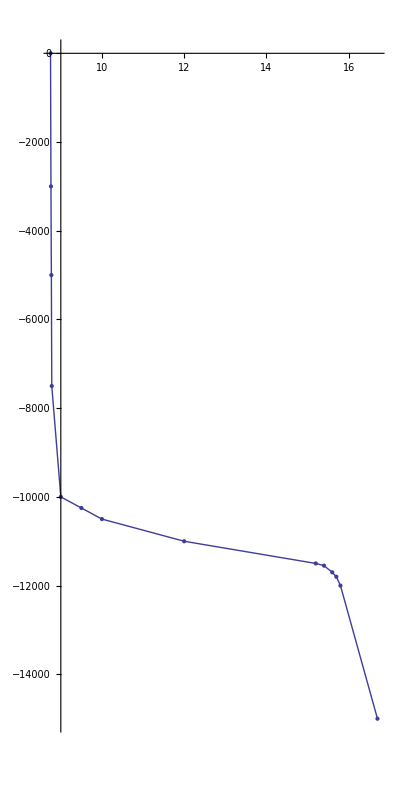

```mathematica
listPP={{8.75,0},{8.76,-3000},{8.77,-5000},{8.78,-7500},{9,-10000},{9.5,-10250},{10,-10500},{12,-11000},{15.2,-11500},{15.4,-11550},{15.6,-11700},{15.7,-11800},{15.8,-12000},{16.7,-15000}}
ListLinePlot[listPP,Mesh->All,AspectRatio->2]
```

```mathematica
LinearEq[pt1_,pt2_]:=Block[{y,x,temp,temp2,temp3},
temp=(pt2[[2]]-pt1[[2]])/(pt2[[1]]-pt1[[1]])(x-pt1[[1]])+pt1[[2]];
temp2=temp/.x->pt1[[1]];
temp3=temp/.x->pt2[[1]];
y=Piecewise[{{pt1[[1]],temp2>0},{pt2[[1]],temp3<pt2[[2]]}},temp];
Return[y]
]
```

```mathematica
eq[x_,Pts_]:=Block[{eq,vecpp,vecfp,i},
vecpp={};
vecfp={};
For[i=1,i<=Length[Pts]-1,i++,
eq=LinearEq[Pts[[i]],Pts[[i+1]]];
TF=CheckPoint[x,Pts[[i]][[1]],Pts[[i+1]][[1]] ];
If[TF,Return[eq]];
];
];
```

```mathematica
eq[9,PtsPorePressure]
```

-10000-209.459 (-8.1+x)

```mathematica
PtsPorePressure={{8,0},{8.1,-10000},{15.5,-11550},{16.2,-15000}};
PtsFracPressure={{11,0},{17,-11000},{18,-15000}};
OperationalWindow[PtsPorePressure_,PtsFracPressure_]:=Block[{eq,vecpp,vecfp,i},
vecpp={};
vecfp={};
For[i=1,i<=Length[PtsPorePressure]-1,i++,
eq=LinearEq[PtsPorePressure[[i]],PtsPorePressure[[i+1]]];
TF=CheckPoint[x,PtsPorePressure[[i]][[1]],PtsPorePressure[[i+1]][[1]] ];
AppendTo[vecpp,eq];
];
For[i=1,i<=Length[PtsFracPressure]-1,i++,
eq=LinearEq[PtsFracPressure[[i]],PtsFracPressure[[i+1]]];
AppendTo[vecfp,eq];
];
{vecpp,vecfp}
];
```

```mathematica
CheckPoint[x_,x1_,x2_]:=Block[{bound=0,i},
If[x1<x<x2,
Return[True];
,
Return[False];
];
];
```

```mathematica
ManageEquations[2,7,10]
```

False

```mathematica
PtsPorePressure[[2]][[1]]
PtsPorePressure[[3]][[1]]
```

8.1

15.5

```mathematica
listPP={{8.75,0},{8.76,-3000},{8.77,-5000},{8.78,-7500},{9,-10000},{9.5,-10250},{10,-10500},{12,-11000},{15.2,-11500},{15.4,-11550},{15.6,-11700},{15.7,-11800},{15.8,-12000},{16.7,-15000}};
```

```mathematica
PtsFracPressure[[2]][[2]]
```

-11000

```mathematica
OperationalWindow[listPP,PtsFracPressure]/.x->16.3
```

{{-2.265×10^6,-1.511×10^6,-1.8875×10^6,-92954.5,-13650.,-13650.,-12075.,-11671.9,-11775.,-12225.,-12400.,-13000.,-13666.7},{-9716.67,-8200.}}

```mathematica
OperationalWindow[listPP,PtsFracPressure][[1]][[1]]
```

-300000. (-8.75+x)

```mathematica
If[Abs[(OperationalWindow[listPP,PtsFracPressure][[1]][[1]]/.x->pt) -  (OperationalWindow[listPP,PtsFracPressure][[2]][[1]]/.x->pt)],(OperationalWindow[listPP,PtsFracPressure][[2]][[1]]/.x->pt)]
```

If[Abs[5500/3 (-11+pt)-300000. (-8.75+pt)],OperationalWindow[listPP,PtsFracPressure]⟦2⟧⟦1⟧/.x→pt]

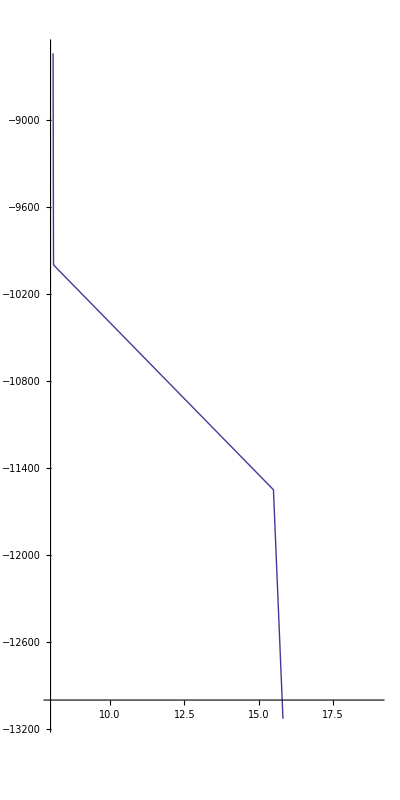

```mathematica
ratio=2;
Plot[eq[x,PtsPorePressure],{x,8,19},AspectRatio->ratio]
```

```mathematica
LinearEq[PtsPorePressure[[1]],PtsPorePressure[[2]]]
```

0

```mathematica
PtsPorePressure[[1]]
PtsPorePressure[[2]]
```

{8,0}

{8.1,-10000}

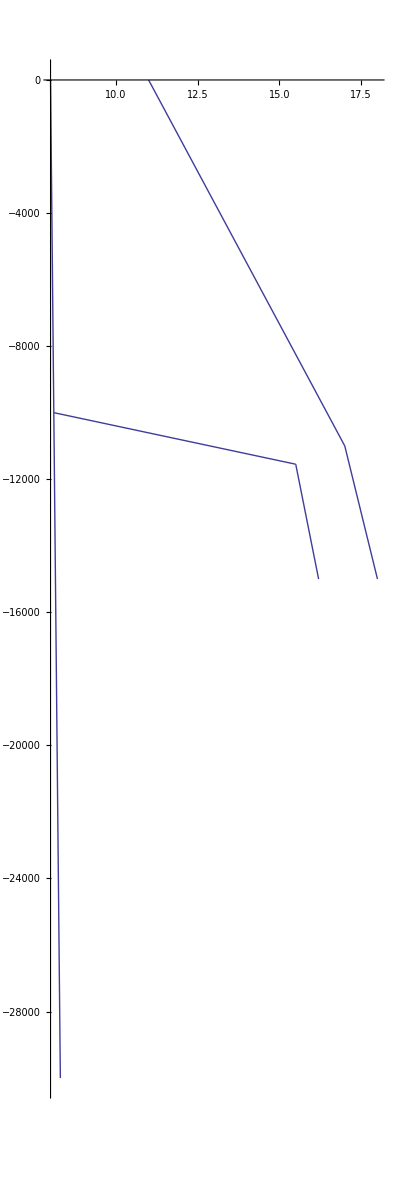

```mathematica
ratio=3;
eq1=LinearEq[{8,0},{8.1,-10000}];
pl1=Plot[eq1,{x,8,8.3},AspectRatio->ratio];
eq2=LinearEq[{8.1,-10000},{15.5,-11550}];
pl2=Plot[eq2,{x,8.1,15.5},AspectRatio->ratio];
eq3=LinearEq[{15.5,-11550},{16.2,-15000}];
pl3=Plot[eq3,{x,15.5,16.2},AspectRatio->ratio];
eq4=LinearEq[{11,0},{17,-11000}];
pl4=Plot[eq4,{x,11,17},AspectRatio->ratio];
eq5=LinearEq[{17,-11000},{18,-15000}];
pl5=Plot[eq5,{x,17,18},AspectRatio->ratio];
Show[pl1,pl2,pl3,pl4,pl5,PlotRange->All]
```

```mathematica
eq1
eq2
eq3
eq4
eq5
```

Piecewise[{{0, x<8}, {-100000. (-8+x), True}}]

Piecewise[{{-10000, x<8.1}, {-10000-209.459 (-8.1+x), True}}]

Piecewise[{{-11550, x<15.5}, {-11550-4928.57 (-15.5+x), True}}]

Piecewise[{{0, x<11}, {-5500/3 (-11+x), True}}]

Piecewise[{{-11000, x<17}, {-11000-4000 (-17+x), True}}]

```mathematica
eq5/.x->16
eq4/.x->16.
```

-11000

-9166.67